```mathematica
∑_(n=1)^∞ 1/n^s + nv
```

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
Expand[Expand[(x+1)^2]*Expand[(x+1)^2]]
```

```mathematica
1+4 x+6 x^2+4 x^3+x^4
Factor[x^6-1]
```

1+4 x+6 x^2+4 x^3+x^4

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
List[a,b,c]
```

{a,b,c}

```mathematica
x = 9
```

9

```mathematica
x=.
```

```mathematica
anEq= {3x*x, x^2,x+x*x*x-y+l(a+x+y)}
```

{3 x^2,x^2,x+x^3-y+l (a+x+y)}

```mathematica
anEq[[2]]
```

x^2

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
expand(%)
```

expand (1+x)^2

```mathematica
1+x+x^2/.x->2-y;(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
t=1+x^2;
```

```mathematica
t/.x->2
```

```mathematica
5Simplify[x^2+2 x+1]
```

5 (1+x)^2

```mathematica
Simplify[Gamma[x] Gamma[1-x]]
```

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
D[x^2+y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
(*gadient*)D[x^2+y^2,{{x,y}}]
```

{2 x,2 y}

```mathematica
f= a*Cos[n x];D[f,{x,7}]
```

a n^7 Sin[n x]

```mathematica
Dt[x^2+c y^2]
```

y^2 Dt[c]+2 x Dt[x]+2 c y Dt[y]

```mathematica
Integrate[x b[x]^2,b[x]]
```

```mathematica
Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]
```

{1/((1+x^2)^2),1/((1+x^2)^2)}

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x];
y[x]+2 y'[x]+y[0]/.%
```

```mathematica
{1+ⅇ^-x C[1]+y[0]+2 y'[x]}
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[{y'[x]==a y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(a x)}}

```mathematica
DSolve[y''[x]+Cos[x] y[x]==0,y,x]
```

{{y→Function[{x},C[1] MathieuC[0,-2,x/2]+C[2] MathieuS[0,-2,x/2]]}}

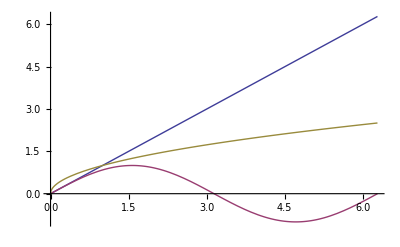

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

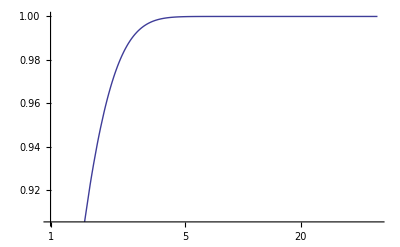

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

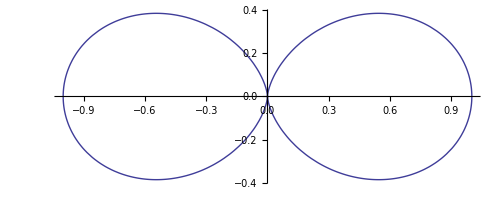

```mathematica
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
```

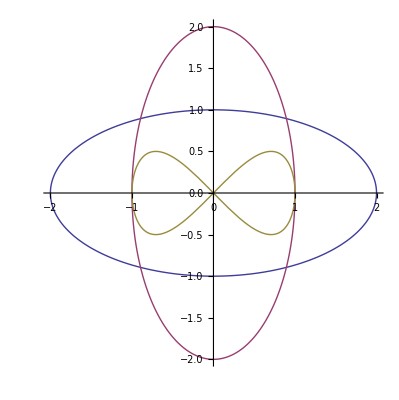

```mathematica
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]},{Sin[t],Sin[t] Cos[t]}},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],Log[r^(1/2)]},{r,0.1,1},{t,0,2 Pi}]
```